# Nanobot Theory : Data Analysis and Plotting

#### Yibin Jiang, Abhishek Sharma Cronin Lab University of Glasgow

```mathematica
deviationslLLP[ave_,dev_,opts:OptionsPattern[]]:=Module[{
fill=Join@@(Thread[Range[Length@ave]->List/@(Length[ave] #+Range[Length@ave])]&/@{1,2}),
apd=Style[#,Opacity[0]]&/@(ave+dev),
amd=Style[#,Opacity[0]]&/@(ave-dev),p1,p2},
p1=ListLinePlot[Join@@{ave,apd,amd},Filling->fill,opts]
]
```

```mathematica
dipoleLength=Quantity[0.41,"nm"];
d=QuantityMagnitude[10^-3 dipoleLength]; 
wavelength = Table[0.44+0.01i,{i,26}];
wavelength =Flatten@{wavelength,Table[0.518+0.002*i,{i,26}]};
wavelengthU = DeleteDuplicates[wavelength];
wavelengthS = 1000*Table[0.45+0.25/1000*i,{i,1000}];
```

```mathematica
wvindex = Flatten@Table[Flatten@Position[wavelength,(Sort@wavelengthU)⟦i⟧]⟦1⟧,{i,Length[wavelengthU]}];
wavelength=wavelength⟦wvindex⟧;
```

```mathematica
plotUVVis[index_]:= Block[{Au,structure,reffi,tempData,intp,plot1,plot2,fig},
position⟦deleteIndex⟦index⟧⟧ =!position⟦deleteIndex⟦index⟧⟧ ;
Au = Pick[data,position];
reffi=((3/(4π))d^3 Length@Au )^(1/3);
tempData=Transpose[{1000*wavelength,UVdata⟦All,1+index⟧/(π reffi^2)}];
intp=Interpolation[tempData,InterpolationOrder->2];
intensityS = intp[wavelengthS];
max=Position[intensityS,Max[intensityS]];
Return[{wavelengthS⟦Flatten@max⟧⟦1⟧,intensityS⟦Flatten@max⟧⟦1⟧}]]
```

```mathematica
informationAll = Table[
baseDirectory=NotebookDirectory[];
data=Import[baseDirectory<>"/data1/dipoles.csv"];
UVdata = Import[baseDirectory<>"/data"<>ToString[repeat]<>"/combined_data"<>ToString[repeat]<>".csv"];
deleteIndex = 1+Flatten@IntegerPart@N@Import[baseDirectory<>"/data"<>ToString[repeat]<>"/changed_dipole_index.csv"];
position = Table[True,{i,Length@data}];

index = 0;
Au = data;
reffi=(3/(4π)d^3 Length@Au )^(1/3);
tempData=Transpose[{1000*wavelength,UVdata⟦All,1+index⟧/(π reffi^2)}];
intp=Interpolation[tempData,InterpolationOrder->2];
intensityS = intp[wavelengthS];
max=Position[intensityS,Max[intensityS]];
information = {{wavelengthS⟦Flatten@max⟧⟦1⟧,intensityS⟦Flatten@max⟧⟦1⟧}};
Table[
p1=plotUVVis[index];
information=Append[information,p1],{index,1,Length[deleteIndex]}];
information,{repeat,1,3}];
```

```mathematica
data1 = Table[informationAll⟦repeat⟧⟦All,1⟧,{repeat,3}];
data2 =  Table[informationAll⟦repeat⟧⟦All,2⟧,{repeat,3}];
```

```mathematica
Dimensions@data1⟦1⟧
```

{14775}

```mathematica
Dimensions@data1⟦2⟧
```

{14165}

```mathematica
Dimensions@data1⟦3⟧
```

{14619}

```mathematica
mean1= Flatten@{
Mean[{data1⟦1⟧⟦1;;14165⟧,data1⟦2⟧,data1⟦3⟧⟦1;;14165⟧}],
Mean[{data1⟦1⟧⟦14166;;14619⟧,data1⟦3⟧⟦14166;;14619⟧}],
Mean[data1⟦1⟧⟦14620;;⟧]};
std1= Flatten@{
StandardDeviation[{data1⟦1⟧⟦1;;14165⟧,data1⟦2⟧,data1⟦3⟧⟦1;;14165⟧}],
StandardDeviation[{data1⟦1⟧⟦14166;;14619⟧,data1⟦3⟧⟦14166;;14619⟧}],
StandardDeviation[data1⟦1⟧⟦14620;;⟧]};
```

```mathematica
mean2= Flatten@{
Mean[{data2⟦1⟧⟦1;;14165⟧,data2⟦2⟧,data2⟦3⟧⟦1;;14165⟧}],
Mean[{data2⟦1⟧⟦14166;;14619⟧,data2⟦3⟧⟦14166;;14619⟧}],
Mean[data2⟦1⟧⟦14620;;⟧]};
std2= Flatten@{
StandardDeviation[{data2⟦1⟧⟦1;;14165⟧,data2⟦2⟧,data2⟦3⟧⟦1;;14165⟧}],
StandardDeviation[{data2⟦1⟧⟦14166;;14619⟧,data2⟦3⟧⟦14166;;14619⟧}],
StandardDeviation[data2⟦1⟧⟦14620;;⟧]};
```

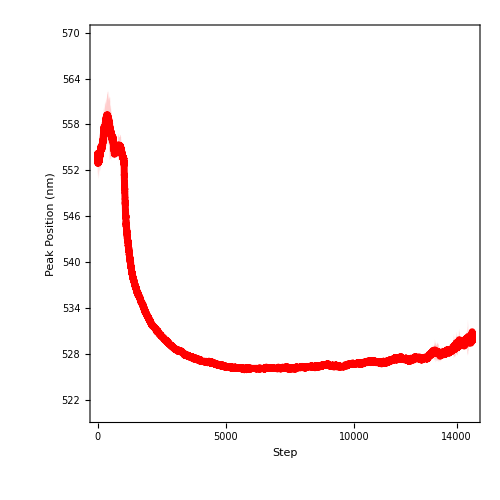

```mathematica
f1 = deviationslLLP[
{mean1},
{std1},
ImagePadding->80,
DataRange->{0,Length[mean1]-1},
PlotStyle->{{Red,Thickness[0.01]},
{Blue,Thickness[0.01]}},
AspectRatio->1,
LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->22]},
FrameTicks->{{Automatic,Automatic},{{0,5000,10000,14000},Automatic}},
Frame->{True,True,True,False},
FrameLabel->{"Step","Peak Position (nm)"},
Frame->True,
FrameStyle->{{{Thick,Red},Thick},{Thick,Thick}},
FrameTicksStyle->{{Thick,Thick},{{Thick},Thick}},
ImageSize->500,PlotRange->{520,570}]
```

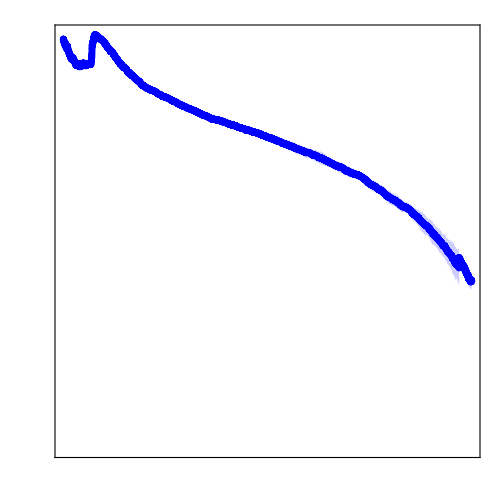

```mathematica
f2= deviationslLLP[{mean2},{std2},
ImagePadding->80,
DataRange->{0,Length[mean2]-1},
PlotStyle->{{Blue,Thickness[0.01]},{Blue,Thickness[0.01]}},
AspectRatio->1,
LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->22]},
Axes->False,
Frame->{False,False,False,True},
FrameLabel->{{None,"Maximum Extinction"},{None,None}},
FrameTicks->{{None,All},{None,None}},
Frame->True,
FrameStyle->{{None,{Thick,Blue}},{None,None}},
FrameTicksStyle->{{Thick,Thick},{Thick,Thick}},ImageSize->500,PlotRange->All]
```

```mathematica
Dimensions@mean1
Dimensions@mean2
```

{14620}

{14620}

```mathematica
f = Overlay[{f1,f2}];
Export[NotebookDirectory[]<>"/f.png",f,ImageResolution->300];
```

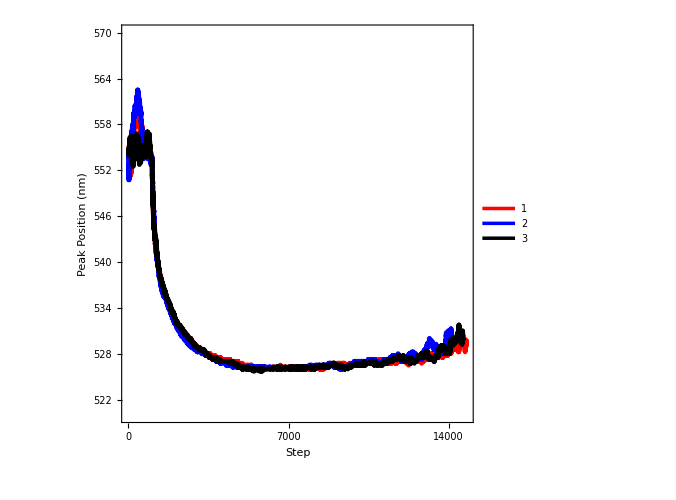

```mathematica
f=ListLinePlot[
Table[Transpose[{Range[0,Length[data1⟦i⟧]-1],data1⟦i⟧}],{i,3}],
PlotStyle->{{Red,Thickness[0.007]},
{Blue,Thickness[0.007]},
{Black,Thickness[0.007]},
{Cyan,Thickness[0.007]}},
FrameTicks->{{Automatic,Automatic},{{0,7000,14000},Automatic}},
PlotLegends->Placed[{"1","2","3"},{0.8,0.8}],
AspectRatio->1,
LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->22]},
FrameLabel->{"Step","Peak Position (nm)"},
Frame->True,
FrameStyle->{{Thick,Thick},{Thick,Thick}},
FrameTicksStyle->{{Thick,Thick},{{Thick},Thick}},
ImageSize->500,PlotRange->{520,570}]
Export[NotebookDirectory[]<>"/f1.png",f,ImageResolution->300];
```

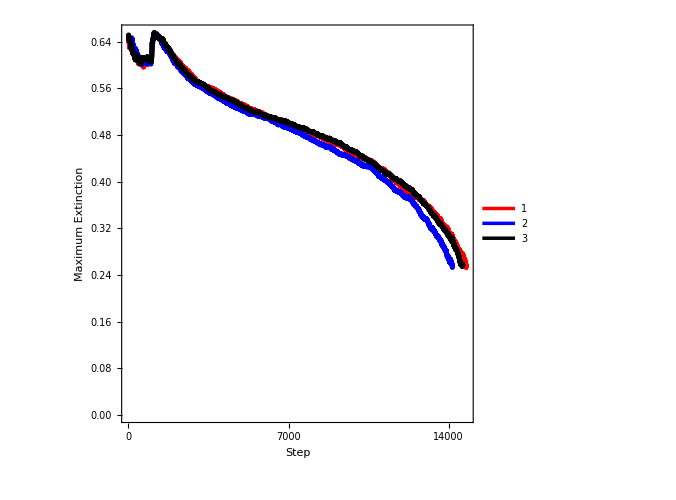

```mathematica
f = ListLinePlot[
Table[Transpose[{Range[0,Length[data2⟦i⟧]-1],data2⟦i⟧}],{i,3}],
PlotStyle->{{Red,Thickness[0.007]},
{Blue,Thickness[0.007]},
{Black,Thickness[0.007]},
{Cyan,Thickness[0.007]}},
FrameTicks->{{Automatic,Automatic},{{0,7000,14000},Automatic}},
PlotLegends->Placed[{"1","2","3"},{0.1,0.2}],
AspectRatio->1,
LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->22]},
FrameLabel->{"Step","Maximum Extinction"},
Frame->True,
FrameStyle->{{Thick,Thick},{Thick,Thick}},
FrameTicksStyle->{{Thick,Thick},{{Thick},Thick}},
ImageSize->500,PlotRange->All]
Export[NotebookDirectory[]<>"/f2.png",f,ImageResolution->300];
```

```mathematica
Position[data1⟦1⟧,Max[data1⟦1⟧]]
```

{{320},{349},{358}}

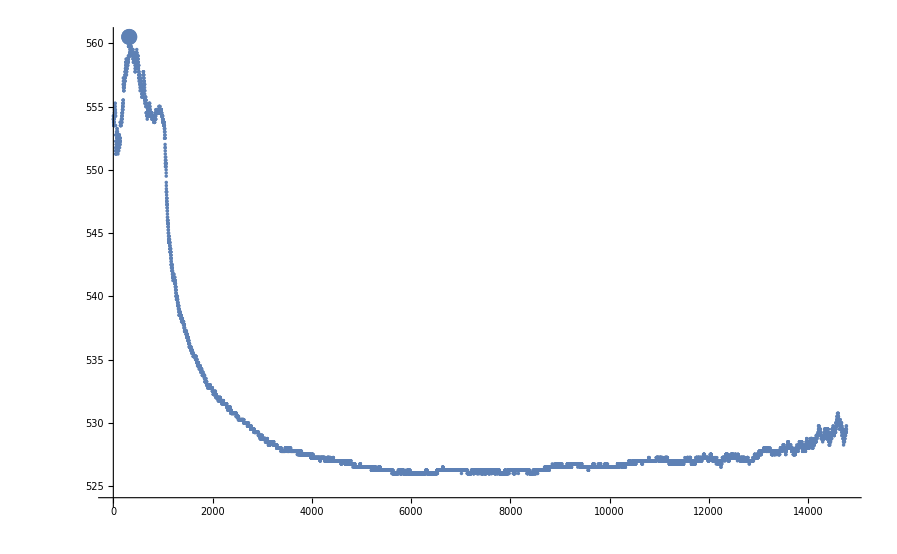

```mathematica
Show[{ListPlot[data1⟦1⟧,PlotRange->All],
ListPlot[{{320,data1⟦1⟧⟦320⟧}},PlotRange->All]}]
```

```mathematica
Position[data2⟦1⟧,Max[data2⟦1⟧]]
```

{{1128}}

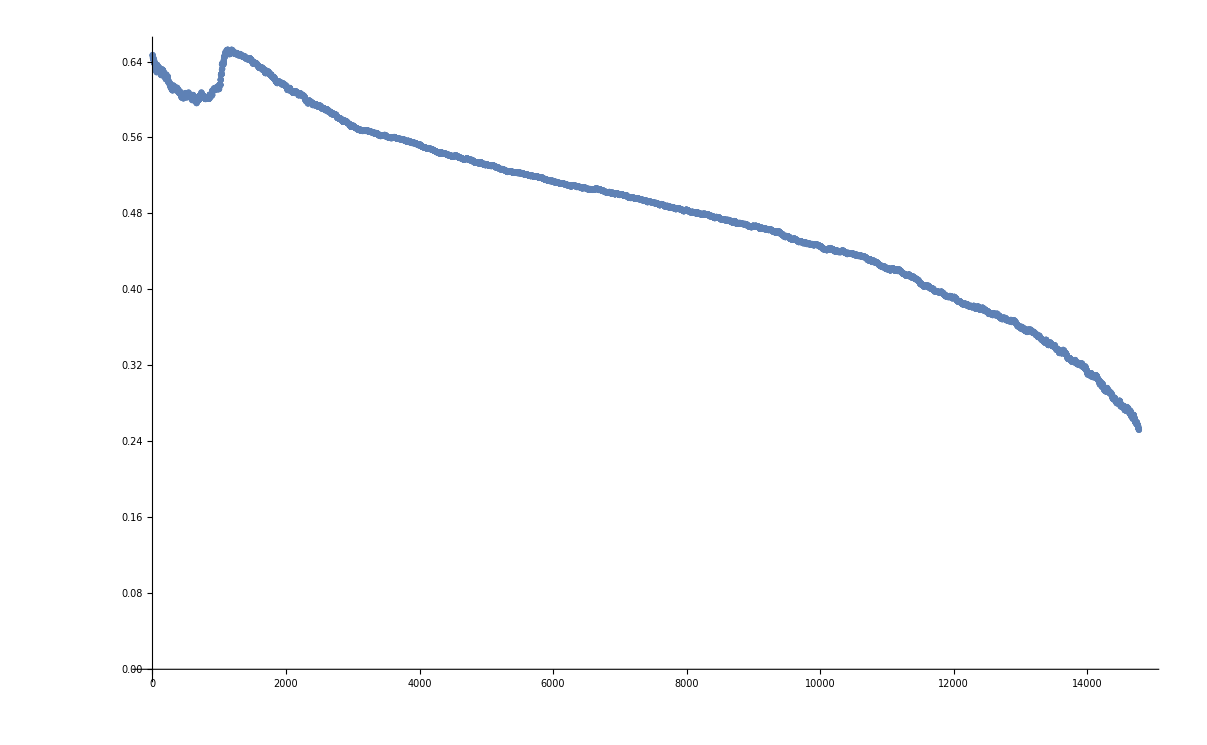

```mathematica
Show[{ListPlot[data2⟦1⟧,PlotRange->All],
ListPlot[{{1128,data2⟦1⟧⟦1128⟧}},PlotRange->All,PlotMarkers->{Red, Large}]}]
```